{-17.017,7.68358,1.09019,-4.14736,13.5555,8.3443,4.64107,-0.716235,-2.27707,-1.76026,-6.7436,3.39526,9.86359,-3.37139,0.30519,3.95811,-9.54024,-6.98479,9.68112,9.38565,2.61881,13.6119,-4.05184,6.64862,-11.4778,0.256033,4.18511,13.6626,12.1157,13.4721,11.4662,-0.942828,9.04135,17.3915,-6.69084,-0.386484,-3.9528,0.0395283,-0.752284,4.6123,17.4765,15.5695,15.5189,16.4991,19.9257,4.08177,0.470208,2.43115,11.1484,-5.01274,0.942253,-1.48669,14.9562,13.0693,-10.3792,2.24834,-11.3384,-4.52878,-2.92652,5.78586,5.73713,-17.0746,8.88048,-0.893413,5.35183,21.141,11.3026,0.436009,6.36085,1.92463,-11.0061,14.6555,9.7458,0.327427,-0.635442,-1.1725,-5.47178,-1.96834,18.402,7.4003,2.31702,3.33571,5.90937,8.13243,-11.6623,-16.9271,10.6094,0.758655,-4.58669,6.99511,11.1569,11.3567,-13.9912,0.394466,14.8965,8.97274,-6.42202,-1.38198,12.2811,9.83122}

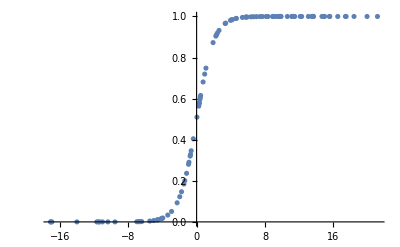

```mathematica
<<NeuralNetworks`;
n = 100;
x = RandomReal[{-2*π, 2*π}, n];
𝒫=WhiteNoiseProcess[];
x = RandomVariate[NormalDistribution[π,10],100];
y = Evaluate[LogisticSigmoid[x]];
data = Transpose@{x,y};
ListPlot[data]
```